# Movimento de Projétil 3D

## com resistência do ar

## Introdução

Neste trabalho será analisado o movimento tridimensional de um projeto. Será considerado o lançamento oblíquo de um ponto  material sob a ação da gravidade local g⃗ e de uma força de atrito proporcional à velocidade instantânea do projétil, f⃗ = - kv⃗. Utilizando para este fim todo o nosso potencial de imaginação combinado aos recursos gráficos do software Wolfram Mathematica 9.0, exploramos ao máximo a cinemática do movimento proposto.

## Limpando todas as variáveis

Limpando as variáveis do problema.

```mathematica
Off[Remove::"rmnsm"];
Off[General::"spell1"];
Off[General::"spell"];
Off[Solve::"ifun"];
```

```mathematica
Remove["`*"];
$Line=0;
```

```mathematica
Names["`*"]
```

{}

## Configurações gráficas

Modificando algumas configurações gráficas dos comandos do Mathematica.

```mathematica
SetOptions[{ListPlot,ParametricPlot},
GridLines->Automatic, 
GridLinesStyle->Directive[Thickness[0.004],Black,Dashed],
Frame->True,
FrameStyle->Directive[Thickness[0.004],Black,18,Bold],
Background->White,
ImageSize->600];
```

```mathematica
SetOptions[{ListPointPlot3D,ParametricPlot3D},
Background->White,
ImageSize->600];
```

```mathematica
SetOptions[{Plot},ImageSize->600
PlotRange->{0,All},GridLines->Automatic,AxesOrigin->{0,0},Filling->Bottom,PlotStyle->{Blue,Thick},ImageSize->600,PlotLegends->"Expressions",Frame->True,FrameStyle->Directive[Black,18]];
```

## Equações Cinemáticas

A partir de um abordagem dinâmica do problema, temos:

R⃗ = m g⃗- K v⃗  ⟹ m a⃗ = m g⃗ - K v⃗ ⟹
 a⃗=g⃗-k v⃗  (1)

As equações gerais da cinemática são dadas por:

a⃗ = (d v⃗)/dt   e   v⃗ = (d r⃗)/dt ⟹^(1)
(d^2 r⃗)/(d t^2) = g⃗ - k(d r⃗)/dt

Note que as equações independem do sistema de coordenadas adotado.

## Definindo as componentes da aceleração

Adotamos o sistema de coordenadas cartesianas devido à simplificação na representação do vetor
 aceleração gravitacional e à maior familiaridade com o sistema.

Escrevendo as equações diferenciais da aceleração em cada componente (x, y, z):

(d^2 OverVector[r_x])/(d t^2) = -k(d OverVector[r_x])/dt /  (d^2 OverVector[r_y])/(d t^2) = -k(d OverVector[r_y])/dt / (d^2 OverVector[r_z])/(d t^2)= -g⃗ - k(d OverVector[r_z])/dt  ⟹^(Notação)
(r̈)_x = -k(r^˙)_x /(r̈)_y = -k(r^˙)_y /(r̈)_z = -g - k(r^˙)_z

Observe que convencionamos a gravidade com sentido negativo (contrário) em relação ao eixo z do sistema de coordenadas.

```mathematica
dif = {x''[t]==-k*x'[t],y''[t]==-k*y'[t],z''[t]==-g-k*z'[t]}
```

{x''[t]==-k x'[t],y''[t]==-k y'[t],z''[t]==-g-k z'[t]}

## Definindo a velocidade inicial

Adotamos a escrita da velocidade inicial segundo coordenadas esféricas por uma questão de estética.
Escrevendo a velocidade inicial segundo suas componentes esféricas:

v⃗ = v_x(û)_x + v_y(û)_y + v_z(û)_z
v_x=vcosbsina
v_y=v sina sinb
v_z=vcosa

```mathematica
eq =
{
x[0]==0, x'[0]==v*Sin[a]*Cos[b],
y[0] == 0, y'[0] ==v*Sin[a]*Sin[b],
z[0]==0,z'[0]==v*Cos[a]
}
```

{x[0]==0,x'[0]==v Cos[b] Sin[a],y[0]==0,y'[0]==v Sin[a] Sin[b],z[0]==0,z'[0]==v Cos[a]}

## Resolvendo a equação diferencial da posição

Resolvendo as equações diferenciais da posição, obtemos:

r(t)=(1-ⅇ^-kt)/k[v_x,v_y,(g/k-gt/(1-ⅇ^-kt)+v_z)]

Vetor posição em coordenadas cartesianas em função do tempo.
Note que vx, vy e vz são as componentes x, y, z da velocidade inicial.

```mathematica
solucao1 = DSolve[Join[eq,dif],{x[t],y[t],z[t]},t]
```

{{x[t]→(ⅇ^(-k t) (-1+ⅇ^(k t)) v Cos[b] Sin[a])/k,y[t]→(ⅇ^(-k t) (-1+ⅇ^(k t)) v Sin[a] Sin[b])/k,z[t]→-(ⅇ^(-k t) (g-ⅇ^(k t) g+ⅇ^(k t) g k t+k v Cos[a]-ⅇ^(k t) k v Cos[a]))/k^2}}

## Componentes do vetor posição

As componentes do vetor posição ficam da seguinte forma:

OverVector[r_x](t) = (1-ⅇ^-kt)/k v_x (û)_x

```mathematica
x[t_]=solucao1[[1,1,2]]
```

(ⅇ^(-k t) (-1+ⅇ^(k t)) v Cos[b] Sin[a])/k

OverVector[r_y](t) = (1-ⅇ^-kt)/k v_y (û)_y

```mathematica
y[t_]=solucao1[[1,2,2]]
```

(ⅇ^(-k t) (-1+ⅇ^(k t)) v Sin[a] Sin[b])/k

```mathematica
Subscript[r, z]^(->)(t) = ((1-ⅇ^-kt)/k) [ g/k-gt/(1-ⅇ^-kt)+Subscript[v, z] ]  Subscript[û, z]
```

```mathematica
z[t_]=solucao1[[1,3,2]]
```

-(ⅇ^(-k t) (g-ⅇ^(k t) g+ⅇ^(k t) g k t+k v Cos[a]-ⅇ^(k t) k v Cos[a]))/k^2

## Definindo movimento “sem” resistência do ar

Muitos problemas de física consideram a resistência do ar desprezível. É o que faremos nas próximas atribuições,
 considerando a constante da resistência do ar k = 0.001.
As componentes do vetor posição ficam da seguinte forma:

```mathematica
x0[t_]=x[t]/.k->0.001
```

1000. ⅇ^(-0.001 t) (-1+ⅇ^(0.001 t)) v Cos[b] Sin[a]

```mathematica
y0[t_]=y[t]/.k->0.001
```

1000. ⅇ^(-0.001 t) (-1+ⅇ^(0.001 t)) v Sin[a] Sin[b]

```mathematica
z0[t_]=z[t]/.k->0.001
```

-1.×10^6 ⅇ^(-0.001 t) (g-ⅇ^(0.001 t) g+0.001 ⅇ^(0.001 t) g t+0.001 v Cos[a]-0.001 ⅇ^(0.001 t) v Cos[a])

## Definindo resistência do ar k = d

Declaremos também uma função do vetor posição que dependa do parâmetro k = d, de forma a comparar 
posteriormente o efeito da variação da resistência do ar na trajetória do projétil.

As componentes do vetor posição ficam da seguinte forma:

```mathematica
xd[t_]=x[t]/.k->d
```

(ⅇ^(-d t) (-1+ⅇ^(d t)) v Cos[b] Sin[a])/d

```mathematica
yd[t_]=y[t]/.k->d
```

(ⅇ^(-d t) (-1+ⅇ^(d t)) v Sin[a] Sin[b])/d

```mathematica
zd[t_]=z[t]/.k->d
```

-(ⅇ^(-d t) (g-ⅇ^(d t) g+d ⅇ^(d t) g t+d v Cos[a]-d ⅇ^(d t) v Cos[a]))/d^2

## Definindo a função posição

A função posição é uma função do vetor posição em relação a todos os parâmetros do problema:
O vetor velocidade e as suas componentes, a gravidade local e a resistência do ar.
Será utilizada posteriormente para ilustrar o efeito de cada um destes parâmetros na trajetória do projétil.

```mathematica
X[t_,alpha_,beta_,vel_,grav_,air_]=x[t]/.{a->alpha, b->beta,v->vel,g->grav,k->air}
```

(ⅇ^(-air t) (-1+ⅇ^(air t)) vel Cos[beta] Sin[alpha])/air

```mathematica
Y[t_,alpha_,beta_,vel_,grav_,air_]=y[t]/.{a->alpha, b->beta,v->vel,g->grav,k->air}
```

(ⅇ^(-air t) (-1+ⅇ^(air t)) vel Sin[alpha] Sin[beta])/air

```mathematica
Z[t_,alpha_,beta_,vel_,grav_,air_]=z[t]/.{a->alpha, b->beta,v->vel,g->grav,k->air}
```

-(ⅇ^(-air t) (grav-ⅇ^(air t) grav+air ⅇ^(air t) grav t+air vel Cos[alpha]-air ⅇ^(air t) vel Cos[alpha]))/air^2

## Definindo as constantes

Em que “a”, “b” e “v” são as componentes esféricas do vetor velocidade, “g” é a aceleração da gravidade local e “k” é o parâmetro da resistência do ar. Definimos essas constantes a priori de forma a ter um parâmetro, uma “noção” da ordem de grandeza das variáveis do problema que estamos tratando: dimensões cotidianas.

```mathematica
a=3.141/6;  (*30.ba*)
b=3.141/3; (*60.ba*)
v=10;               (*10 m/s = 36 km/h*)
g=9.81; (* 9.81 m/s^2*)
k=1; (* Não fazemos a menor ideia do efeito de k sobre o movimento por enquanto. É o nosso objetivo descobrir como ele afeta toda a cinemática do problema *)
```

## Cálculo do tempo de voo

Comparemos o tempo de voo do projétil para algumas constantes de resistência do ar:

Tempo de voo com elevadíssima resistência do ar (k = 15):

```mathematica
tempo= Solve[zd[t]==0,t]/.d->15
```

{{t→0.949515}}

```mathematica
td15 = tempo[[1,1,2]]
```

0.949515

Tempo de voo com elevada resistência do ar (k = 5):

```mathematica
tempo= Solve[zd[t]==0,t]/.d->5
```

{{t→1.07791}}

```mathematica
td5 = tempo[[1,1,2]]
```

1.07791

Tempo de voo com resistência do ar (k = 1):

```mathematica
tempo= Solve[z[t]==0,t]
```

{{t→8.81416×10^-16},{t→1.43412}}

```mathematica
tfinal = tempo[[2,1,2]]
```

1.43412

Tempo de voo com baixa resistência do ar (k = 0.1):

```mathematica
tempo= Solve[zd[t]==0,t]/.d->0.1
```

{{t→1.71661}}

```mathematica
td01 = tempo[[1,1,2]]
```

1.71661

Tempo de voo com quase nula resistência do ar (k = 0.01):

```mathematica
tempo= Solve[zd[t]==0,t]/.d->0.01
```

{{t→1.76053}}

```mathematica
td001 = tempo[[1,1,2]]
```

1.76053

Tempo de voo “sem” resistência do ar (k = 0.001):

```mathematica
Tempo=Solve[z0[t]==0,t]
```

{{t→-6.60174×10^-11},{t→1.76518}}

```mathematica
Tfinal=Tempo[[2,1,2]]
```

1.76518

Representando graficamente os resultados obtidos:

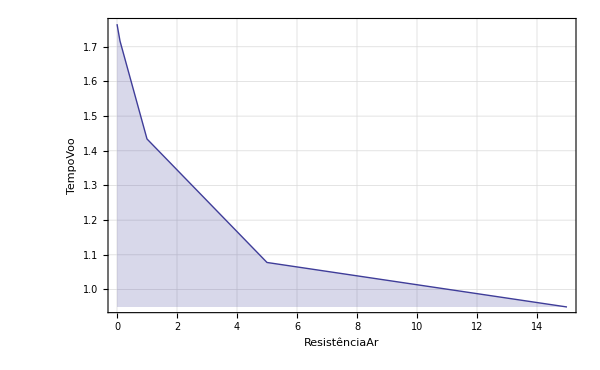

```mathematica
ListPlot[{{0.001,Tfinal},{0.01,td001},{0.1,td01},{1,tfinal},{5,td5},{15,td15}}, PlotRange->Automatic,Filling->Axis,ImageSize->600,Joined->True,FrameLabel->{ResistênciaAr,TempoVoo}]
```

De fato, a expressão geral para o cálculo do Tempo de Voo do projétil é dada por:

T = (1+(d v_z)/G+ProductLog[-ⅇ^(-(1+(d v_z)/G))(1+(d v_z)/G)])/d | v_z=v Cos[A]

```mathematica
Time=Solve[Z[t,alpha,beta,vel,grav,air]==0,t]/.{alpha->A,beta->B,vel->V,grav->G,air->d}
```

{{t→(G+d V Cos[A]+G ProductLog[-(ⅇ^(-1-(d V Cos[A])/G) (G+d V Cos[A]))/G])/(d G)}}

```mathematica
TempoVoo[d_]=Time[[1,1,2]]/.{A->a,B->b,V->v,G->g,d->d}
```

(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))/d

O que nos leva à seguinte curva:

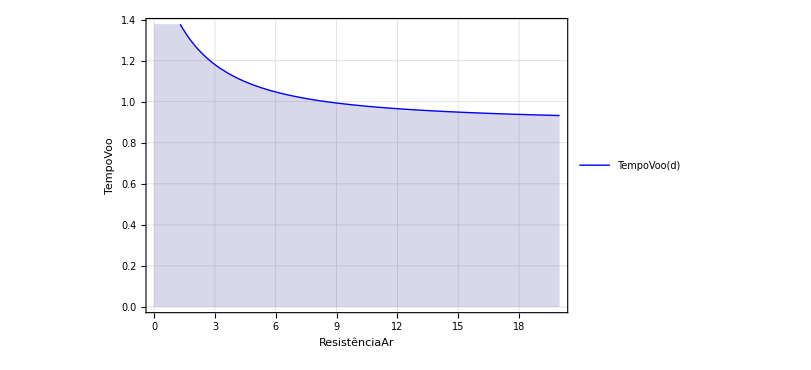

```mathematica
Plot[TempoVoo[d],{d,0,20},FrameLabel->{ResistênciaAr,TempoVoo }]
```

## Cálculo da altura máxima

Comparemos agora a altura máxima alcançada pelo projétil para algumas constantes de resistência do ar:

Altura máxima com resistência do ar (k = 1):

Tempo de voo até a altura máxima:

```mathematica
tempohmax = Solve[z'[t]==0,t]
```

{{t→0.632786}}

```mathematica
tempohMax = tempohmax[[1,1,2]]
```

0.632786

(Tempo de voo até a altura máxima)/(Tempo total de voo):

```mathematica
percenttempohmax=tempohMax/tfinal
```

0.441237

Altura máxima:

```mathematica
hmax=z[tempohMax]
```

2.45312

Altura máxima sem resistência do ar (k = 0.001):

Tempo de voo até a altura máxima:

```mathematica
TempoHmax=Solve[z0'[t]==0,t]
```

{{t→0.882459}}

```mathematica
tempoHmax=TempoHmax[[1,1,2]]
```

0.882459

Altura máxima:

```mathematica
Hmax=z0[tempoHmax]
```

3.82082

A expressão para o cálculo do tempo de voo até a altura máxima é:

t=Log[1+(d v_z)/G]/d |  v_z=v Cos[A]

```mathematica
Time=Solve[D[Z[t,alpha,beta,vel,grav,air], t]==0,t]/.{alpha->A,beta->B,vel->V,grav->G,air->d}
```

{{t→Log[(G+d V Cos[A])/G]/d}}

A expressão geral para o cálculo da altura máxima atingida pelo projétil é dada por:

H=v_z/d(1-(d v_z)/G Log[1+(d v_z)/G])  |  v_z=v Cos[A]

```mathematica
HMAX[d_] = Z[Time[[1,1,2]],alpha,beta,vel,grav,air]/.{alpha->A,beta->B,vel->V,grav->G,air->d}
```

-(G (-(d V Cos[A] (G+d V Cos[A]))/G+(G+d V Cos[A]) Log[(G+d V Cos[A])/G]))/(d^2 (G+d V Cos[A]))

```mathematica
Time=Solve[D[Z[t,alpha,beta,vel,grav,air], t]==0,t]/.{alpha->a,beta->b,vel->v,grav->g,air->d}
```

{{t→Log[0.101937 (9.81+8.66075 d)]/d}}

```mathematica
AlturaMax[d_]=Z[Time[[1,1,2]],alpha,beta,vel,grav,air]/.{alpha->a,beta->b,vel->v,grav->g,air->d}
```

-1/(d^2 (9.81+8.66075 d))9.81 (9.81+8.66075 d-1. (9.81+8.66075 d)-0.882849 d (9.81+8.66075 d)+1. (9.81+8.66075 d) Log[0.101937 (9.81+8.66075 d)])

O que nos leva à seguinte curva:

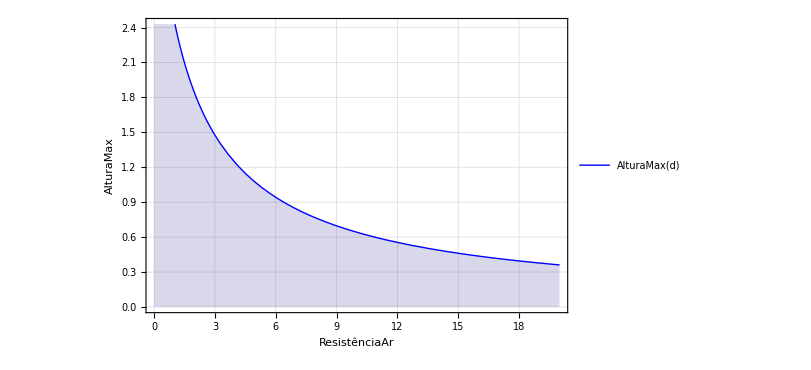

```mathematica
Plot[AlturaMax[d],{d,0,20},FrameLabel->{ResistênciaAr,AlturaMax }]
```

Calculando ainda a razão q entre o tempo de voo até a altura máxima e o tempo de voo total:

q = (Tempo até altura máxima)/(Tempo de voo total) ⟹
 q = Log[1+(d v_z)/G]/((1+(d v_z)/G)+ProductLog[-ⅇ^(-(1+(d v_z)/G))(1+(d v_z)/G)])  ⟹
q=Log[λ]/(λ+ProductLog[-λⅇ^-λ]) |  λ=(1+(d v_z)/G)

```mathematica
q = ( (G+d V Cos[A]+G ProductLog[-(ⅇ^(-1-(d V Cos[A])/G) (G+d V Cos[A]))/G])/(d G))/(Log[(G+d V Cos[A])/G]/d)
```

(G+d V Cos[A]+G ProductLog[-(ⅇ^(-1-(d V Cos[A])/G) (G+d V Cos[A]))/G])/(G Log[(G+d V Cos[A])/G])

O que nos leva à seguinte curva:

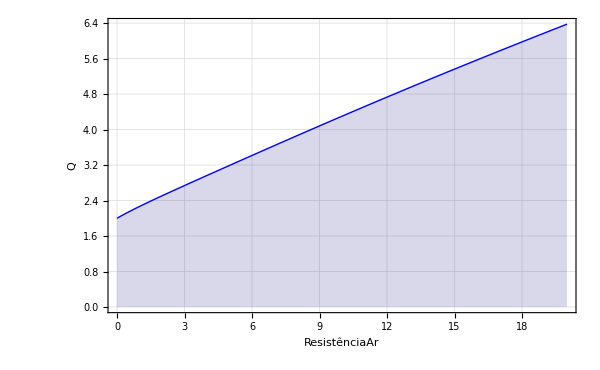

```mathematica
Plot[(G+d V Cos[A]+G ProductLog[-(ⅇ^(-1-(d V Cos[A])/G) (G+d V Cos[A]))/G])/(G Log[(G+d V Cos[A])/G])/.{A->a,B->b,V->v,G->g},{d,0.001,20},PlotLegends->"",FrameLabel->{ResistênciaAr,Q}]
```

## Cálculo do alcance

Comparemos agora o alcance do projétil para algumas constantes de resistência do ar:

Alcance máximo com resistência do ar (k = 15):

```mathematica
alcance = Sqrt[(xd[TempoVoo[d]])^2+(yd[TempoVoo[d]])^2]/.d->15
```

0.333276

Alcance máximo com resistência do ar (k = 10):

```mathematica
alcance = Sqrt[(xd[TempoVoo[d]])^2+(yd[TempoVoo[d]])^2]/.d->10
```

0.499887

Alcance máximo com resistência do ar (k = 5):

```mathematica
alcance = Sqrt[(xd[TempoVoo[d]])^2+(yd[TempoVoo[d]])^2]/.d->5
```

0.995266

Alcance máximo com resistência do ar (k = 1):

```mathematica
distTotal=Sqrt[(x[tfinal])^2+(y[tfinal])^2]
```

3.80772

Alcance máximo sem resistência do ar (k = 0.001):

```mathematica
DisTotal=Sqrt[x0[Tfinal]^2+y0[Tfinal]^2]
```

8.8166

A expressão geral do Alcance máximo do projétil é dada por :

A = (1-ⅇ)^-dT/d √(v_x^2+v_y^2) | T=TempoVoo

```mathematica
Alcance=Sqrt[(X[T,alpha,beta,vel,grav,air])^2+(Y[T,alpha,beta,vel,grav,air])^2] /.{alpha->A,beta->B,vel->V,grav->G,air->d}
```

√((ⅇ^(-2 d T) (-1+ⅇ^(d T))^2 V^2 Cos[B]^2 Sin[A]^2)/d^2+(ⅇ^(-2 d T) (-1+ⅇ^(d T))^2 V^2 Sin[A]^2 Sin[B]^2)/d^2)

```mathematica
Alcanced[d_]=(1-ⅇ^(-d T))/d v √(Cos[b]^2 Sin[a]^2+ Sin[b]^2 Sin[a]^2)/.T->TempoVoo[d]
```

(4.99914 (1-ⅇ^(-0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))))/d

O que nos leva à seguinte curva:

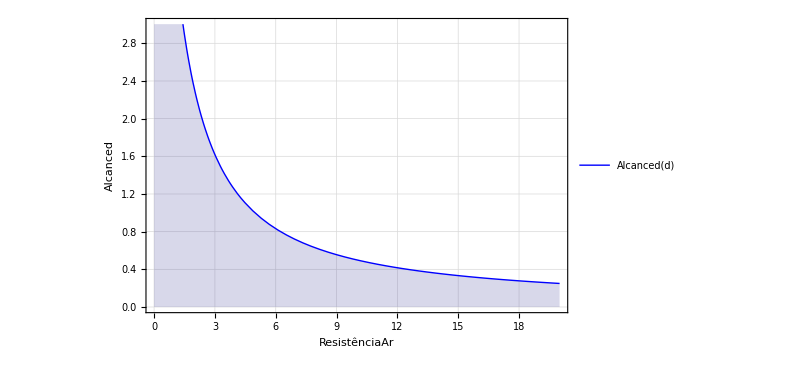

```mathematica
Plot[Alcanced[d],{d,0,20},FrameLabel->{ResistênciaAr,Alcanced}]
```

## Cálculo da velocidade final

Cálculo da velocidade final do projétil no movimento com resistência do ar (k = 1):

```mathematica
vxfinal=x'[tfinal]
```

0.595916

```mathematica
vyfinal=y'[tfinal]
```

1.03169

```mathematica
vzfinal=z'[tfinal]
```

-5.40795

```mathematica
vfinal=Sqrt[vxfinal^2+vyfinal^2+vzfinal^2]
```

5.53764

Calculando a velocidade final do projétil, tem-se que:

V_f = ⅇ^-dT √((G(1-ⅇ^dT)/d+v_z)^2+v^2-v_z^2) | T=TempoVoo

```mathematica
Sqrt[(D[X[t,alpha,beta,vel,grav,air], t])^2+(D[Y[t,alpha,beta,vel,grav,air], t])^2+(D[Z[t,alpha,beta,vel,grav,air], t])^2]/.{alpha->A,beta->B,vel->V,grav->G,air->d}
```

√(((ⅇ^(-d t) (G-ⅇ^(d t) G+d ⅇ^(d t) G t+d V Cos[A]-d ⅇ^(d t) V Cos[A]))/d-(ⅇ^(-d t) (d^2 ⅇ^(d t) G t-d^2 ⅇ^(d t) V Cos[A]))/d^2)^2+(V Cos[B] Sin[A]-ⅇ^(-d t) (-1+ⅇ^(d t)) V Cos[B] Sin[A])^2+(V Sin[A] Sin[B]-ⅇ^(-d t) (-1+ⅇ^(d t)) V Sin[A] Sin[B])^2)

```mathematica
Vf[d_]=Sqrt[(D[X[t,a,b,v,g,d], t])^2+(D[Y[t,a,b,v,g,d], t])^2+(D[Z[t,a,b,v,g,d], t])^2]/.t->TempoVoo[d]
```

√((4.32889-4.32889 ⅇ^(-0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])) (-1+ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))))^2+(2.50043-2.50043 ⅇ^(-0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])) (-1+ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))))^2+(1/d ⅇ^(-0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])) (9.81+8.66075 d-9.81 ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))-8.66075 d ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))+1. ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])) (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))-1/d^2 ⅇ^(-0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])) (0.-8.66075 d^2 ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)]))+1. d ⅇ^(0.101937 (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])) (9.81+8.66075 d+9.81 ProductLog[-0.101937 (9.81+8.66075 d) ⅇ^(-1-0.882849 d)])))^2)

O que nos leva à seguinte curva:

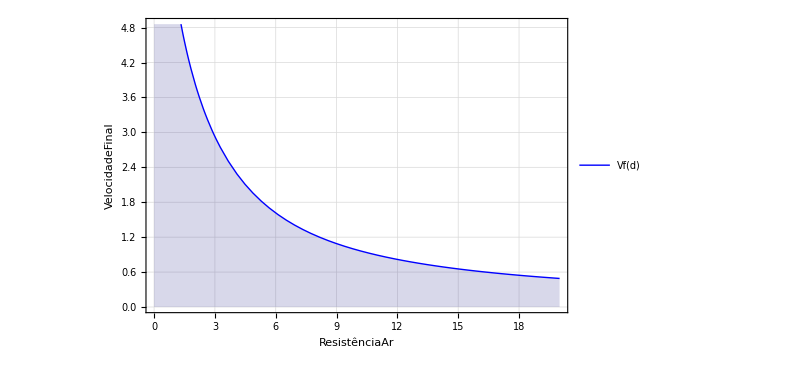

```mathematica
Plot[Vf[d],{d,0,20},FrameLabel->{ResistênciaAr,VelocidadeFinal}]
```

## Trajetória do projétil

## Movimento 2D do projétil no plano XZ

Com interatividade da variação do tempo

Os movimentos teórico e prático ilustram a trajetória com os parâmetros pré-definidos anteriormente, em que a curva teórica representa o movimento sem resistência do ar e a curva prática o movimento com resistência do ar, em um plano bidimensional que no caso é o plano XZ.

```mathematica
Manipulate[
  Show
[
           {
	ListPlot[ {x[t],z[t]}/. solucao1 ,PlotStyle->{PointSize[.03],Blue},PlotRange->All,
PlotLegends->PointLegend[{"Prático"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],
           FrameLabel->{{Altura,None},{Alcanced,"Plano XZ"}}],
	ListPlot[ {X[t,a,b,v,g,air],Z[t,a,b,v,g,air]}/. solucao1 ,PlotStyle->{PointSize[.03],Purple},PlotRange->All,
PlotLegends->PointLegend[{"Dinâmico"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],
           FrameLabel->{{Altura,None},{Alcanced,"Plano XZ"}}],
	ListPlot[ {x0[t],z0[t]}/. solucao1 , PlotStyle->{PointSize[.03],Red},PlotRange->All,
PlotLegends->PointLegend[{"Teórico"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],
           FrameLabel->{{Altura,none},{Alcanced,"Plano XZ"}}],
           ParametricPlot[ {x[t],z[t]} /. solucao1 ,{t,0,tfinal},PlotStyle->{Blue,Thick}],
 ParametricPlot[ {X[t,a,b,v,g,air],Z[t,a,b,v,g,air]} /. solucao1 ,{t,0,TempoVoo[air]},PlotStyle->{Purple,Thick}],
  ParametricPlot[ {x0[t],z0[t]} /. solucao1 ,{t,0,Tfinal},PlotStyle->{Red,Dashed,Thick}]
}
],  {t,0,tfinal,.05},{air,0.01,5,.1},ControlPlacement->Top,  SaveDefinitions->True
]
```

## Movimento 2D do projétil no plano YZ

Com interatividade da variação do tempo

Os movimentos teórico e prático ilustram a trajetória com os parâmetros pré-definidos anteriormente, em que a curva teórica representa o movimento sem resistência do ar e a curva prática o movimento com resistência do ar, em um plano bidimensional que no caso é o plano YZ.

```mathematica
Manipulate[
  Show
[
           {
	ListPlot[ {y[t],z[t]}/. solucao1 ,PlotStyle->{PointSize[.03],Blue},PlotRange->All,
PlotLegends->PointLegend[{"Prático"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],
           FrameLabel->{{Altura,None},{Alcanced,"Plano YZ"}}],
	ListPlot[ {Y[t,a,b,v,g,air],Z[t,a,b,v,g,air]}/. solucao1 ,PlotStyle->{PointSize[.03],Purple},PlotRange->All,
PlotLegends->PointLegend[{"Dinâmico"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],
           FrameLabel->{{Altura,None},{Alcanced,"Plano YZ"}}],
	ListPlot[ {y0[t],z0[t]}/. solucao1 , PlotStyle->{PointSize[.03],Red},PlotRange->All,
PlotLegends->PointLegend[{"Teórico"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],
           FrameLabel->{{Altura,none},{Alcanced,"Plano YZ"}}],
           ParametricPlot[ {y[t],z[t]} /. solucao1 ,{t,0,tfinal},PlotStyle->{Blue,Thick}],
 ParametricPlot[ {Y[t,a,b,v,g,air],Z[t,a,b,v,g,air]} /. solucao1 ,{t,0,TempoVoo[air]},PlotStyle->{Purple,Thick}],
  ParametricPlot[ {y0[t],z0[t]} /. solucao1 ,{t,0,Tfinal},PlotStyle->{Red,Dashed,Thick}]
}
],  {t,0,tfinal,.05},{air,0.01,5,.1},ControlPlacement->Top,  SaveDefinitions->True
]
```

## Movimento 3D do projétil

Comparando diferentes intensidades de resistência do ar.

As diversas curvas dessa simulação representa movimentos cujos parâmetros foram definidos anteriormente, variando apenas o parâmetro da resistência do ar (k) para o efeito de comparação das trajetórias pelo usuário.

```mathematica
Show[{
ParametricPlot3D[{xd[t],yd[t],zd[t]}/.{d->0.1},{t,0,Tfinal},PlotRange->{0,All},
PlotLegends->PointLegend[{"k=0.1"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue], PlotStyle->{Black,Thick}],
ParametricPlot3D[{xd[t],yd[t],zd[t]}/.{d->1},{t,0,tfinal},
PlotLegends->PointLegend[{"k=1"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],  PlotStyle->{Purple,Thick}],
ParametricPlot3D[{xd[t],yd[t],zd[t]}/.{d->2}, {t, 0, tfinal}, PlotLegends->PointLegend[{"k=2"},LegendMarkerSize->10,LegendFunction->Frame,
Background->LightBlue],PlotStyle->{Blue,Thick}],
ParametricPlot3D[{xd[t],yd[t],zd[t]}/.{d->3},{t,0,tfinal},PlotLegends->PointLegend[{"k=3"},LegendMarkerSize->10,LegendFunction->Frame,
Background->LightBlue],PlotStyle->{Cyan,Thick}]
}]
```

-Graphics3D-

## Movimento 3D dinâmico do projétil

Com interatividade de todos os parâmetros

Os movimentos teórico e prático ilustram a trajetória com os parâmetros pré-definidos anteriormente, em que a curva teórica representa o movimento sem resistência do ar e a curva prática o movimento com resistência do ar.
	Por motivos lúdicos, a simulação oferece ao usuário ferramentas para alterar os parâmetros básicos do problema, como o vetor velocidade inicial, o vetor gravidade e o parâmetro da resistência do ar (qualitativamente).

```mathematica
Manipulate[
Show[
{
ParametricPlot3D[{x0[t],y0[t],z0[t]}/.solucao1,{t,0,Tfinal},PlotStyle->{Red,Thick},PlotRange->{0,All},PlotLegends->{"Teórico"}],
ParametricPlot3D[{x[t],y[t],z[t]}/.solucao1,{t,0,Tfinal},PlotStyle->{Blue,Thick},PlotRange->{0,All},PlotLegends->{"Prático"}],
ParametricPlot3D[{X[t,alpha,beta,vel,grav,air],Y[t,alpha,beta,vel,grav,air],Z[t,alpha,beta,vel,grav,air]}/.solucao1,{t,0,Tfinal},PlotStyle->{Purple,Thick},PlotRange->{0,All},PlotLegends->{"Dinâmico"}]
}
],{alpha,0,π/2,.1},{beta,0,π/2,.1},{vel,0,20,1},{grav,0,20,1},{air,0.01,5,.1},ControlPlacement->Top,  SaveDefinitions->True
]
```

## Movimento 3D dinâmico do projétil

Com interatividade na variação do tempo

Os movimentos teórico e prático ilustram a trajetória com os parâmetros pré-definidos anteriormente, em que a curva teórica representa o movimento sem resistência do ar e a curva prática o movimento com resistência do ar. Nessa simulação há a apresentação de um ponto da curva em função do parâmetro tempo para efeitos lúdicos e didáticos, simulando como um observador veria o acontecimento.

```mathematica
Manipulate[
  Show
[
      {
	ListPointPlot3D[{x[t],y[t],z[t]}/.solucao1 ,PlotStyle->{PointSize[.02],Red}],
	ListPointPlot3D[{x0[t],y0[t],z0[t]}/.solucao1 ,PlotStyle->{PointSize[.02],Blue}],
	ListPointPlot3D[{X[t,a,b,v,g,air],Y[t,a,b,v,g,air],Z[t,a,b,v,g,air]}/.solucao1 ,PlotStyle->{PointSize[.02],Purple}],
	ParametricPlot3D[{x[t],y[t],z[t]}/.solucao1,{t,0,tfinal},
PlotLegends->PointLegend[{"Prático"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],PlotStyle->{Red,Thick}],
	ParametricPlot3D[{x0[t],y0[t],z0[t]}/.solucao1,{t,0,Tfinal},
PlotLegends->PointLegend[{"Teórico"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue],PlotStyle->{Blue,Thick}],
ParametricPlot3D[{X[t,a,b,v,g,air],Y[t,a,b,v,g,air],Z[t,a,b,v,g,air]}/.solucao1,{t,0,TempoVoo[air]},PlotStyle->{Purple,Thick},PlotLegends->PointLegend[{"Dinâmico"},LegendMarkerSize->10,LegendFunction->Frame,Background->LightBlue]]
}
],  {t,0,tfinal,.025},{air,0.01,5,.1},ControlPlacement->Top,  SaveDefinitions->True
]
```

## Final do notebook

## Felipe Tuyama Marcos Rodrigo